```mathematica
LogNeg2=Table[Max[0,-Log[Min[Abs[Eigenvalues[ⅈ Σ . σPT2]]]]],{t,3π/20,π/4,π/20000}];
LogNeg3=Table[Max[0,-Log[Min[Abs[Eigenvalues[ⅈ Σ . σPT3]]]]],{t,3π/20,π/4,π/20000}];
```

```mathematica
ListPlot[Table[LogNeg2,{t,3π/20,π/4,π/2000}],Joined->True,PlotRange->All]
```

-Graphics-

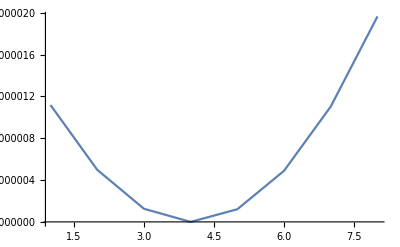

```mathematica
ListPlot[{LogNeg2[[1003]],LogNeg2[[1004]],LogNeg2[[1005]],LogNeg2[[1006]],LogNeg2[[1007]],LogNeg2[[1008]],LogNeg2[[1009]],LogNeg2[[1010]]},Joined->True,PlotRange->All]
```

```mathematica
LogNeg2[[1006]]
```

1.08888×10^-11

```mathematica
(*Separable?*)
```

```mathematica
LogNeg3[[1006]]
```

1.47567×10^-6